Solving Poisson equation for Φ(x,y)...

-Graphics-

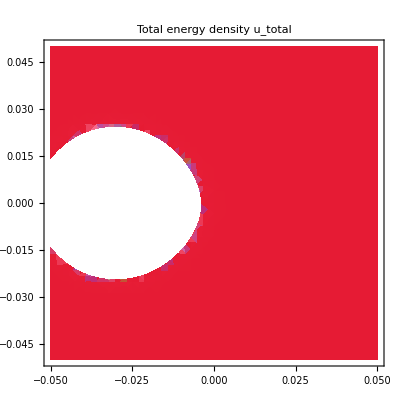

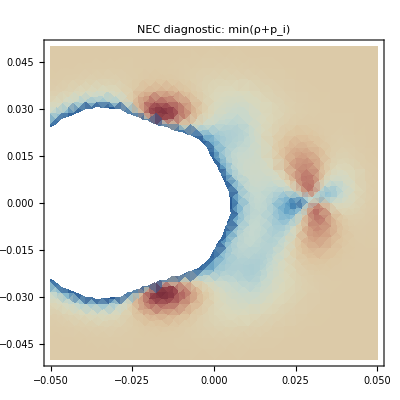

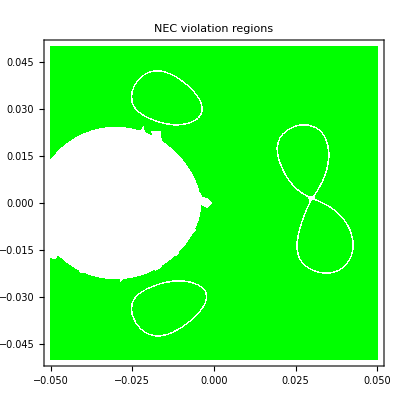

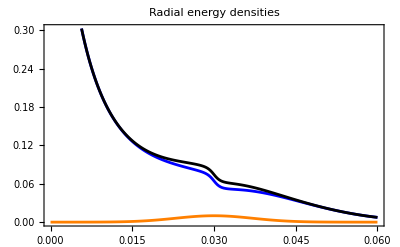

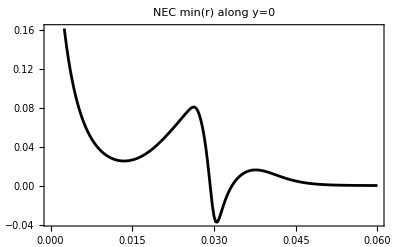

```mathematica
(* =====================================================*)(*0. CLEAN START*)(* =====================================================*)ClearAll["Global`*"];

(* =====================================================*)
(*1. PARAMETERS (YOUR OPTIMIZED SET)*)
(* =====================================================*)

R0=0.03;
wShell=0.01;
d=0.06;
bBI=1.0;
omega=2 Pi 5.0;

bestPars={1.97001,0.685107,4.05734,0.98985,0.753244,0.00139359,-0.902839,3.60618*10^-9};

{A1,A2,phi0,m1,m2,epsY,chir1,chir2}=bestPars;

rho0=10^-2;
betaR0=0.3;
betaT0=0.3;
gammaR=-50.;
gammaT=50.;
t0=0.0;

rPlane[x_,y_]:=Sqrt[x^2+y^2];
L=0.06;

(* =====================================================*)
(*2. VORTEX EM FIELDS*)
(* =====================================================*)

eOneNum[x_?NumericQ,y_?NumericQ,t_?NumericQ,cx_,cy_,A_,phase_,mix_]:=Module[{rx=x-cx,ry=y-cy,rr,g,er,et},rr=Sqrt[rx^2+ry^2];
If[rr<10^-9,{0.,0.,0.},g=Exp[-(rx^2+ry^2)/R0^2];
er={rx/rr,ry/rr,0.};
et={-ry/rr,rx/rr,0.};
A*g*Cos[omega t+phase]*((1-mix)*er+mix*et)]]

bOneNum[x_?NumericQ,y_?NumericQ,t_?NumericQ,cx_,cy_,A_,phase_,chir_]:=Module[{rx=x-cx,ry=y-cy,rr,g,et},rr=Sqrt[rx^2+ry^2];
If[rr<10^-9,{0.,0.,0.},g=Exp[-(rx^2+ry^2)/R0^2];
et={-ry/rr,rx/rr,0.};
A*g*Sin[omega t+phase]*chir*et]]

eFieldNum[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=Module[{c1={-d/2,0.},c2={d/2,epsY}},eOneNum[x,y,t,c1[[1]],c1[[2]],A1,0.,m1]+eOneNum[x,y,t,c2[[1]],c2[[2]],A2,phi0,m2]]

bFieldNum[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=Module[{c1={-d/2,0.},c2={d/2,epsY}},bOneNum[x,y,t,c1[[1]],c1[[2]],A1,0.,chir1]+bOneNum[x,y,t,c2[[1]],c2[[2]],A2,phi0,chir2]]

(* =====================================================*)
(*3. BORN–INFELD INVARIANTS*)
(* =====================================================*)

FInvNum[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=Module[{E=eFieldNum[x,y,t],B=bFieldNum[x,y,t]},0.5*((B.B)-(E.E))]

SNum[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=1+(2*FInvNum[x,y,t])/bBI^2;

LFNum[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=-1/Sqrt[SNum[x,y,t]];

DFieldNum[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=-LFNum[x,y,t]*eFieldNum[x,y,t];

HFieldNum[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=-LFNum[x,y,t]*bFieldNum[x,y,t];

(* =====================================================*)
(*4. BI STRESS–ENERGY TENSOR*)
(* =====================================================*)

stressEnergyBINum[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=Module[{E=eFieldNum[x,y,t],B=bFieldNum[x,y,t],D=DFieldNum[x,y,t],H=HFieldNum[x,y,t],L,u,S,T},L=bBI^2 (1-Sqrt[SNum[x,y,t]]);
u=E.D-L;
S=Cross[E,H];
T=ConstantArray[0.,{4,4}];
T[[1,1]]=u;
T[[1,2;;4]]=S;
T[[2;;4,1]]=S;
Do[Do[T[[i+1,j+1]]=-E[[i]] D[[j]]-B[[i]] H[[j]]+If[i==j,E.D+B.H-L,0],{j,1,3}],{i,1,3}];
T]

(* =====================================================*)
(*5. ANISOTROPIC SHELL MATERIAL*)
(* =====================================================*)

shellProfile[r_]:=Exp[-(r-R0)^2/wShell^2];

rhoShell[x_?NumericQ,y_?NumericQ]:=rho0*shellProfile[rPlane[x,y]];

E2[x_?NumericQ,y_?NumericQ]:=(eFieldNum[x,y,t0].eFieldNum[x,y,t0]);

betaR[x_?NumericQ,y_?NumericQ]:=betaR0+gammaR*E2[x,y];
betaT[x_?NumericQ,y_?NumericQ]:=betaT0+gammaT*E2[x,y];

pRShell[x_?NumericQ,y_?NumericQ]:=betaR[x,y]*rhoShell[x,y];
pTShell[x_?NumericQ,y_?NumericQ]:=betaT[x,y]*rhoShell[x,y];

shellStressTensor[x_?NumericQ,y_?NumericQ]:=Module[{ρ=rhoShell[x,y],pr=pRShell[x,y],pt=pTShell[x,y]},{{ρ,0,0,0},{0,pr,0,0},{0,0,pt,0},{0,0,0,pt}}]

(* =====================================================*)
(*6. TOTAL TENSOR+★ FIX ★ SAFE-MATRIX WRAPPER*)
(* =====================================================*)

Ttot[x_?NumericQ,y_?NumericQ]:=stressEnergyBINum[x,y,t0]+shellStressTensor[x,y];

(*★ FIX ★ ensures Ttot never collapses to a scalar*)
safeMatrix[M_]:=If[MatrixQ[M],M,ConstantArray[0.,{4,4}]];

TtotSafe[x_?NumericQ,y_?NumericQ]:=safeMatrix[Ttot[x,y]];
uTot[x_?NumericQ,y_?NumericQ]:=TtotSafe[x,y][[1,1]];

(* =====================================================*)
(*7. ENERGY CONDITIONS*)
(* =====================================================*)

energyConditionsFromT[T_]:=Module[{ρ,spatial,evals},ρ=T[[1,1]];
spatial=Symmetrize[T[[2;;4,2;;4]]];
evals=Eigenvalues[spatial];
<|"rho"->ρ,"pEigen"->evals,"NECmin"->Min[ρ+evals]|>]

biEC[x_?NumericQ,y_?NumericQ]:=energyConditionsFromT[stressEnergyBINum[x,y,t0]];

shellEC[x_?NumericQ,y_?NumericQ]:=energyConditionsFromT[shellStressTensor[x,y]];

totalEC[x_?NumericQ,y_?NumericQ]:=energyConditionsFromT[TtotSafe[x,y]];

(* =====================================================*)
(*8. SOLVE POISSON FOR φ(x,y)*)
(* =====================================================*)

Print["Solving Poisson equation for Φ(x,y)..."];

(*★ FIX ★ change RHS to uTot[x,y]*)
phiFun=NDSolveValue[{Laplacian[phi[x,y],{x,y}]==-4 Pi*uTot[x,y],phi[-L,y]==0,phi[L,y]==0,phi[x,-L]==0,phi[x,L]==0},phi,{x,-L,L},{y,-L,L},Method->{"PDEDiscretization"->{"FiniteElement"}}];

PhiVal[x_?NumericQ,y_?NumericQ]:=phiFun[x,y];

(* =====================================================*)
(*9. VISUALIZATION*)
(* =====================================================*)

phiPlot=DensityPlot[PhiVal[x,y],{x,-0.05,0.05},{y,-0.05,0.05},ColorFunction->"SolarColors",PlotRange->All,Frame->True,PlotLabel->"Scalar field Φ(x,y)"];

uTotPlot=DensityPlot[uTot[x,y],{x,-0.05,0.05},{y,-0.05,0.05},ColorFunction->"BrightBands",PlotRange->All,Frame->True,PlotLabel->"Total energy density u_total"];

phiPlot
uTotPlot

(* =====================================================*)
(*10. NEC MAP*)
(* =====================================================*)

NECminTotal[x_?NumericQ,y_?NumericQ]:=totalEC[x,y]["NECmin"];

necMap=DensityPlot[NECminTotal[x,y],{x,-0.05,0.05},{y,-0.05,0.05},ColorFunction->"RedBlueTones",PlotLabel->"NEC diagnostic: min(ρ+p_i)"];

necViolationMask=DensityPlot[If[NECminTotal[x,y]<0,-1,1],{x,-0.05,0.05},{y,-0.05,0.05},ColorFunction->(If[#<0,Red,Green]&),PlotRange->{-1,1},PlotLabel->"NEC violation regions"];

necMap
necViolationMask

(* =====================================================*)
(*11. RADIAL PROFILES*)
(* =====================================================*)

rMin=0.;rMax=0.06;nPts=200;

radialData=Table[Module[{x=r,y=0.,Tbi,Tshell,Tt,ECt},Tbi=stressEnergyBINum[x,y,t0];
Tshell=shellStressTensor[x,y];
Tt=TtotSafe[x,y];
ECt=energyConditionsFromT[Tt];
{r,Tbi[[1,1]],Tshell[[1,1]],Tt[[1,1]],ECt["NECmin"]}],{r,rMin,rMax,(rMax-rMin)/nPts}];

rVals=radialData[[All,1]];
rhoBIr=radialData[[All,2]];
rhoShellr=radialData[[All,3]];
rhoTotr=radialData[[All,4]];
NECminTotr=radialData[[All,5]];

rhoLines=ListLinePlot[{Transpose[{rVals,rhoBIr}],Transpose[{rVals,rhoShellr}],Transpose[{rVals,rhoTotr}]},PlotStyle->{Blue,Orange,Black},Frame->True,PlotLabel->"Radial energy densities"];

necLines=ListLinePlot[Transpose[{rVals,NECminTotr}],PlotStyle->Black,Frame->True,PlotLabel->"NEC min(r) along y=0"];

rhoLines
necLines
```